```mathematica
FourierSeries[x^2,x,10]
```

-2 ⅇ^(-ⅈ x)-2 ⅇ^(ⅈ x)+1/2 ⅇ^(-2 ⅈ x)+1/2 ⅇ^(2 ⅈ x)-2/9 ⅇ^(-3 ⅈ x)-2/9 ⅇ^(3 ⅈ x)+1/8 ⅇ^(-4 ⅈ x)+1/8 ⅇ^(4 ⅈ x)-2/25 ⅇ^(-5 ⅈ x)-2/25 ⅇ^(5 ⅈ x)+1/18 ⅇ^(-6 ⅈ x)+1/18 ⅇ^(6 ⅈ x)-2/49 ⅇ^(-7 ⅈ x)-2/49 ⅇ^(7 ⅈ x)+1/32 ⅇ^(-8 ⅈ x)+1/32 ⅇ^(8 ⅈ x)-2/81 ⅇ^(-9 ⅈ x)-2/81 ⅇ^(9 ⅈ x)+1/50 ⅇ^(-10 ⅈ x)+1/50 ⅇ^(10 ⅈ x)+π^2/3

```mathematica
ExpToTrig[%1]
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]-4/49 Cos[7 x]+1/16 Cos[8 x]-4/81 Cos[9 x]+1/25 Cos[10 x]

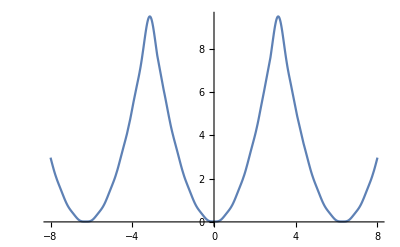

```mathematica
Plot[π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]-4/49 Cos[7 x]+1/16 Cos[8 x]-4/81 Cos[9 x]+1/25 Cos[10 x],{x,-8,8}]
```

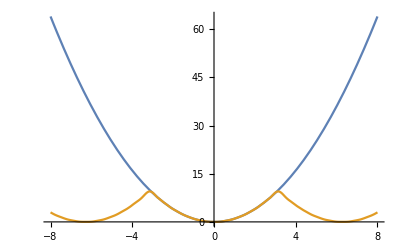

```mathematica
Plot[{x^2,π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]-4/49 Cos[7 x]+1/16 Cos[8 x]-4/81 Cos[9 x]+1/25 Cos[10 x]},{x,-8,8}]
```

```mathematica
FullSimplify[Normalize[D[{x,Out[2]},x]].Normalize[D[{x,x^2},x]],x∈Reals]
```

(315+x (2520 Sin[x]-1260 Sin[2 x]+840 Sin[3 x]-630 Sin[4 x]+504 Sin[5 x]-420 Sin[6 x]+360 Sin[7 x]-315 Sin[8 x]+280 Sin[9 x]-252 Sin[10 x]))/(315 √((1+4 x^2) (1+(-4 Sin[x]+2 Sin[2 x]-4/3 Sin[3 x]+Sin[4 x]-4/5 Sin[5 x]+2/3 Sin[6 x]-4/7 Sin[7 x]+1/2 Sin[8 x]-4/9 Sin[9 x]+2/5 Sin[10 x])^2)))

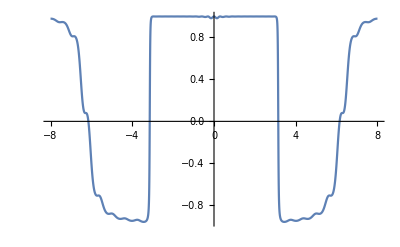

```mathematica
Plot[%5,{x,-8,8}]
```

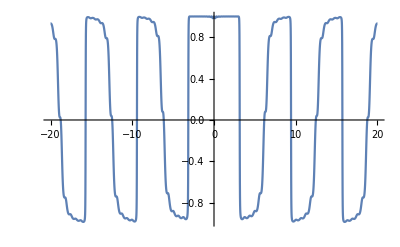

```mathematica
Plot[%5,{x,-20,20}]
```

```mathematica
FourierSeries[x,x,10]
```

ⅈ ⅇ^(-ⅈ x)-ⅈ ⅇ^(ⅈ x)-1/2 ⅈ ⅇ^(-2 ⅈ x)+1/2 ⅈ ⅇ^(2 ⅈ x)+1/3 ⅈ ⅇ^(-3 ⅈ x)-1/3 ⅈ ⅇ^(3 ⅈ x)-1/4 ⅈ ⅇ^(-4 ⅈ x)+1/4 ⅈ ⅇ^(4 ⅈ x)+1/5 ⅈ ⅇ^(-5 ⅈ x)-1/5 ⅈ ⅇ^(5 ⅈ x)-1/6 ⅈ ⅇ^(-6 ⅈ x)+1/6 ⅈ ⅇ^(6 ⅈ x)+1/7 ⅈ ⅇ^(-7 ⅈ x)-1/7 ⅈ ⅇ^(7 ⅈ x)-1/8 ⅈ ⅇ^(-8 ⅈ x)+1/8 ⅈ ⅇ^(8 ⅈ x)+1/9 ⅈ ⅇ^(-9 ⅈ x)-1/9 ⅈ ⅇ^(9 ⅈ x)-1/10 ⅈ ⅇ^(-10 ⅈ x)+1/10 ⅈ ⅇ^(10 ⅈ x)

```mathematica
ExpToTrig[%8]
```

2 Sin[x]-Sin[2 x]+2/3 Sin[3 x]-1/2 Sin[4 x]+2/5 Sin[5 x]-1/3 Sin[6 x]+2/7 Sin[7 x]-1/4 Sin[8 x]+2/9 Sin[9 x]-1/5 Sin[10 x]

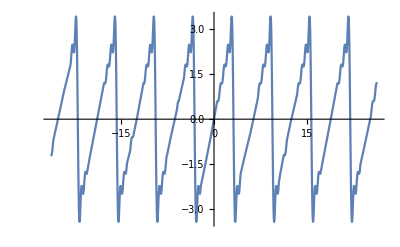

```mathematica
Plot[2 Sin[x]-Sin[2 x]+2/3 Sin[3 x]-1/2 Sin[4 x]+2/5 Sin[5 x]-1/3 Sin[6 x]+2/7 Sin[7 x]-1/4 Sin[8 x]+2/9 Sin[9 x]-1/5 Sin[10 x],{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
FullSimplify[Normalize[D[{x,Out[9]},x]].Normalize[D[{x,x},x]],x∈Reals]
```

(1+2 Cos[x]-2 Cos[2 x]+2 Cos[3 x]-2 Cos[4 x]+2 Cos[5 x]-2 Cos[6 x]+2 Cos[7 x]-2 Cos[8 x]+2 Cos[9 x]-2 Cos[10 x])/(√2 √(1+4 (Cos[x]-Cos[2 x]+Cos[3 x]-Cos[4 x]+Cos[5 x]-Cos[6 x]+Cos[7 x]-Cos[8 x]+Cos[9 x]-Cos[10 x])^2))

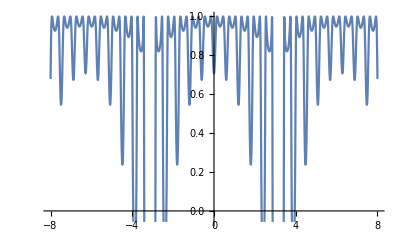

```mathematica
Plot[%11,{x,-8,8}]
```

```mathematica
FullSimplify[Normalize[{x,Out[9]}].Normalize[{x,x}],x∈Reals]
```

(x (2520 Sin[x]-1260 Sin[2 x]+840 Sin[3 x]-630 Sin[4 x]+504 Sin[5 x]+5 (252 x-84 Sin[6 x]+72 Sin[7 x]-63 Sin[8 x]+56 Sin[9 x])-252 Sin[10 x]))/(1260 √2 √(x^2 (x^2+(-2 Sin[x]+Sin[2 x]-2/3 Sin[3 x]+1/2 Sin[4 x]-2/5 Sin[5 x]+1/3 Sin[6 x]-2/7 Sin[7 x]+1/4 Sin[8 x]-2/9 Sin[9 x]+1/5 Sin[10 x])^2)))

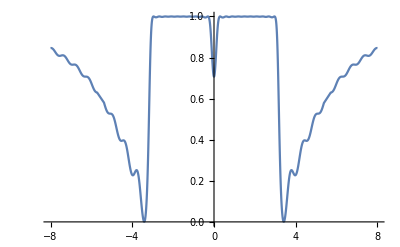

```mathematica
Plot[%13,{x,-8,8}]
```

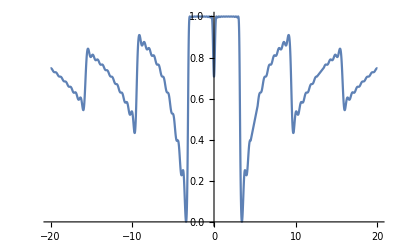

```mathematica
Plot[%13,{x,-20,20}]
```

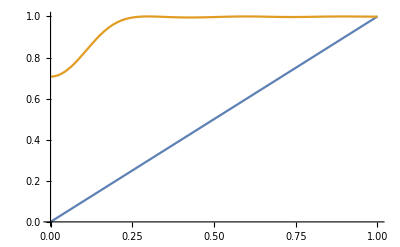

```mathematica
Plot[{x,%13},{x,0,1}]
```

```mathematica
ArcLength[%13,{x,0,1}]
```

$Aborted

```mathematica
NIntegrate[√(D[%13,x]^2+1),{x,0,1}]
```

1.14423